## MPO Tensors

### Square Lattice

#### Vertex Tensor

Starting from the vertex tensor for FPL (for β=0 only)

X[σ_i]=δ(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1) ⅇ^(ⅈ θ (σ_1+σ_2+σ_3+σ_4)/8),

with the angle θ parameterize the θ-term. σ_i=±1, and the labeling convesion as follows.

```mathematica
Graphics[{{Thickness[Absolute[3]],Gray,Rotate[Line[{#,0}&/@{0,1}],#π/2,{0,0}]&/@Range[0,3]},{White,EdgeForm[Black],Disk[{0,0},0.4]},{Text["X",{0,0},{-0.2,0.1}]},
Text["\!\(σ\_"<>ToString[Mod[#,4,1]]<>"\)",RotationMatrix[-#π/2].{-0.8,-0.8}]&/@Range[0,3]},ImageSize->50]
```

-Graphics-

δ term make sure the edges are two-occupied-two-empty by the domain wall (σ_i σ_(i+1)=±1 for domain wall empty/occupation, so they must add to to 0). On the exponent, if ∑σ=0, spins are balanced, domain wall is straight, otherwise more up → positive angle, more down → negative angle.

Tensor code: Q=ⅇ^(ⅈ θ)

```mathematica
Module[{X},
X=Table[KroneckerDelta[σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1]Q^((σ1+σ2+σ3+σ4)/8),{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"1"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[1,2,3,4,6,7,8,9,11,12,13,14],[Q**0.25,Q**0.25,Z1,Q**0.25,Z1,Q**(-0.25),Q**0.25,Z1,Q**(-0.25),Z1,Q**(-0.25),Q**(-0.25)])

#### Make MPO

{3.,1.,1.,1.}

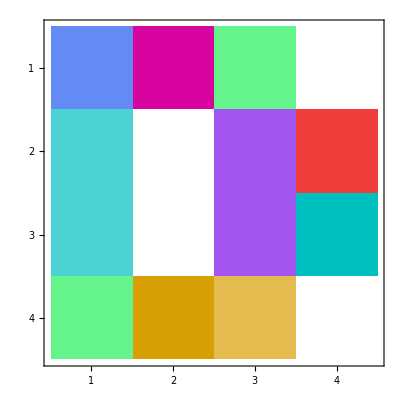
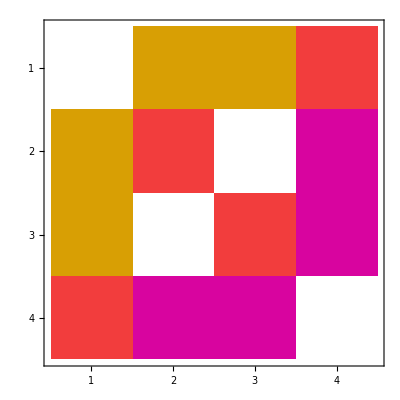

{(-0.353553-0.353553 ⅈ | -0.5
-0.5 | -0.353553+0.353553 ⅈ),(0.5-0.5 ⅈ | 0
0 | 0.5+0.5 ⅈ),(-0.353553+0.353553 ⅈ | 0.-0.5 ⅈ
0.-0.5 ⅈ | 0.353553+0.353553 ⅈ),(0 | 0.707107
-0.707107 | 0)}

```mathematica
Module[{U,S,V,X},
{U,S,V}=SYSVD[TensorLoad["X"]];
U⟦All,{3,4}⟧=U⟦All,{3,4}⟧.Orthogonalize[{{1,2.09370111},{0,1}}];
U⟦All,{2,3,4}⟧=U⟦All,{2,3,4}⟧.Orthogonalize[{{1,-0.707106781,0},{0,1,0},{0,0,1}}];
Print[Normal@Diagonal[S]];
Print[ComplexMatrixPlot/@{U,U.S.Transpose[U]}];
MatrixForm[Partition[#,2]]&/@Transpose[Chop@U]]
```

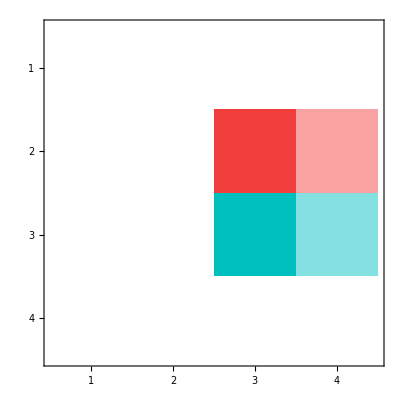

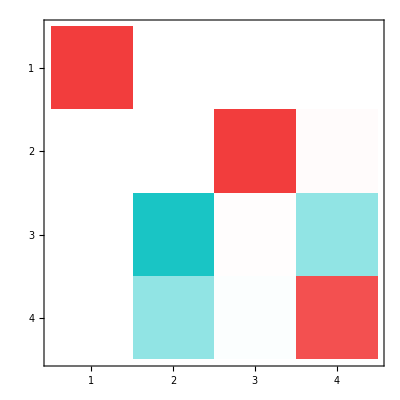
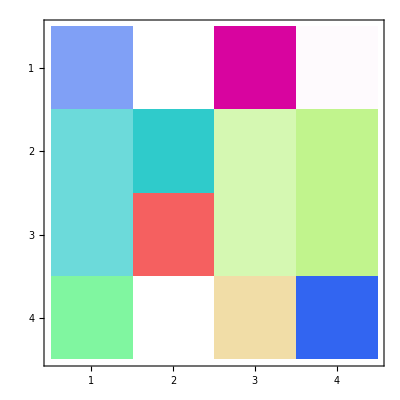
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{U,S,V,Ur,Q,R},
{U,S,V}=SYSVD[TensorLoad["X"]];
Ur=U⟦{1,3,2,4},All⟧;
Print[ComplexMatrixPlot/@{U-Ur}];
{Q,R}=QRDecomposition[Transpose[U-Ur]];
Print[ComplexMatrixPlot/@{Transpose[Q],U=U.Transpose[Q],U.S.Transpose[U]}];]
```

{2.1304+4.44089×10^-16 ⅈ,-0.565198+1.04343 ⅈ,-0.565198-1.04343 ⅈ,1.-2.22045×10^-16 ⅈ}

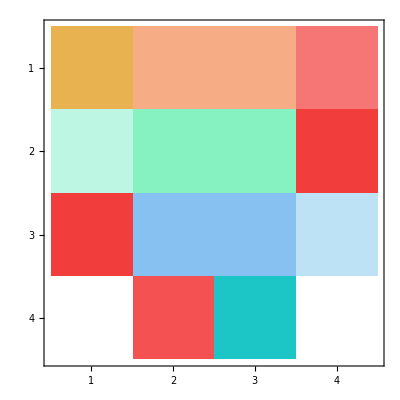
{-Graphics-,-Graphics-}

```mathematica
Module[{s,U,X},
X=TensorLoad["X"];
{s,U}=Eigensystem[X];
Print[s];
Print[ComplexMatrixPlot/@{X,U}]]
```

Verification

```mathematica
Module[{T, A},
 T = Transpose[TensorLoad["T"], {3, 1, 4, 2}];
 A = Map[Abstract, T, {2}];
 Print@MatrixForm@A;
Rationalize@Chop[Plus @@ Tr[Nest[Collect[Inner[CircleTimes, #, A], _σ] &, A, 3], List]]]
```

(0.75 σ[1]+(0.+0.75 ⅈ) σ[3] | -0.0543166 σ[0]+(0.+0.0543166 ⅈ) σ[1]+(0.+0.605103 ⅈ) σ[2]+0.0543166 σ[3] | -0.5 σ[0]-(0.+0.25 ⅈ) σ[1]-0.25 σ[3] | -0.349356 σ[0]+(0.+0.349356 ⅈ) σ[1]-(0.+0.0940791 ⅈ) σ[2]+0.349356 σ[3]
-0.0543166 σ[0]+(0.+0.0543166 ⅈ) σ[1]+(0.+0.605103 ⅈ) σ[2]+0.0543166 σ[3] | (0.+0.00786744 ⅈ) σ[0]+0.484265 σ[1]-0.0876456 σ[2]-(0.+0.00786744 ⅈ) σ[3] | (0.+0.0181055 ⅈ) σ[0]+0.0181055 σ[1]+0.201701 σ[2]-(0.+0.0181055 ⅈ) σ[3] | (0.+0.0506022 ⅈ) σ[0]-0.101204 σ[1]-0.275048 σ[2]-(0.+0.0506022 ⅈ) σ[3]
-0.5 σ[0]-(0.+0.25 ⅈ) σ[1]-0.25 σ[3] | (0.+0.0181055 ⅈ) σ[0]+0.0181055 σ[1]+0.201701 σ[2]-(0.+0.0181055 ⅈ) σ[3] | (0.-0.333333 ⅈ) σ[0]-0.0833333 σ[1]-(0.+0.416667 ⅈ) σ[3] | (0.+0.116452 ⅈ) σ[0]+0.116452 σ[1]-0.0313597 σ[2]-(0.+0.116452 ⅈ) σ[3]
-0.349356 σ[0]+(0.+0.349356 ⅈ) σ[1]-(0.+0.0940791 ⅈ) σ[2]+0.349356 σ[3] | (0.+0.0506022 ⅈ) σ[0]-0.101204 σ[1]-0.275048 σ[2]-(0.+0.0506022 ⅈ) σ[3] | (0.+0.116452 ⅈ) σ[0]+0.116452 σ[1]-0.0313597 σ[2]-(0.+0.116452 ⅈ) σ[3] | (0.+0.325466 ⅈ) σ[0]-0.150932 σ[1]+0.0876456 σ[2]-(0.+0.325466 ⅈ) σ[3])

1/8 σ[0,0,0,0]+1/4 σ[0,0,1,1]+1/4 ⅈ σ[0,0,1,3]-1/4 σ[0,0,2,2]+1/4 ⅈ σ[0,0,3,1]-1/8 σ[0,0,3,3]-1/4 ⅈ σ[0,1,0,3]+1/4 σ[0,1,1,0]+1/4 ⅈ σ[0,1,3,0]-1/4 σ[0,2,2,0]-1/4 ⅈ σ[0,3,0,1]+1/8 σ[0,3,0,3]+1/4 ⅈ σ[0,3,1,0]-1/8 σ[0,3,3,0]+1/4 σ[1,0,0,1]+1/4 ⅈ σ[1,0,0,3]-1/4 ⅈ σ[1,0,3,0]+1/4 σ[1,1,0,0]+1/8 σ[1,1,1,1]+1/4 ⅈ σ[1,1,1,3]-1/8 σ[1,1,2,2]+1/4 ⅈ σ[1,1,3,1]-1/4 σ[1,1,3,3]-1/8 σ[1,2,1,2]-1/8 σ[1,2,2,1]-1/4 ⅈ σ[1,2,2,3]-1/4 ⅈ σ[1,2,3,2]+1/4 ⅈ σ[1,3,0,0]+1/4 ⅈ σ[1,3,1,1]-σ[1,3,1,3]-1/4 ⅈ σ[1,3,2,2]-1/4 σ[1,3,3,1]-1/4 ⅈ σ[1,3,3,3]-1/4 σ[2,0,0,2]-1/8 σ[2,1,1,2]-1/8 σ[2,1,2,1]-1/4 ⅈ σ[2,1,2,3]-1/4 ⅈ σ[2,1,3,2]-1/4 σ[2,2,0,0]-1/8 σ[2,2,1,1]-1/4 ⅈ σ[2,2,1,3]+1/8 σ[2,2,2,2]-1/4 ⅈ σ[2,2,3,1]+1/4 σ[2,2,3,3]-1/4 ⅈ σ[2,3,1,2]-1/4 ⅈ σ[2,3,2,1]+1/4 σ[2,3,3,2]+1/4 ⅈ σ[3,0,0,1]-1/8 σ[3,0,0,3]-1/4 ⅈ σ[3,0,1,0]+1/8 σ[3,0,3,0]+1/4 ⅈ σ[3,1,0,0]+1/4 ⅈ σ[3,1,1,1]-1/4 σ[3,1,1,3]-1/4 ⅈ σ[3,1,2,2]-σ[3,1,3,1]-1/4 ⅈ σ[3,1,3,3]-1/4 ⅈ σ[3,2,1,2]-1/4 ⅈ σ[3,2,2,1]+1/4 σ[3,2,2,3]-1/8 σ[3,3,0,0]-1/4 σ[3,3,1,1]-1/4 ⅈ σ[3,3,1,3]+1/4 σ[3,3,2,2]-1/4 ⅈ σ[3,3,3,1]+1/8 σ[3,3,3,3]

```mathematica
With[{L=4},
Module[{Σs,X,T},
Σs=Tuples[{1,-1},L];
X[{{σ1_,σ2_},{σ4_,σ3_}}]:=Piecewise[{{Exp[ⅈ π/8(σ1+σ2+σ3+σ4)],σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1==0}},0];
T=Table[With[{Σ={Σ1,Σ2}},Times@@(X[Σ⟦All,{#,Mod[#+1,L,1]}⟧]&/@Range[L])],{Σ1,Σs},{Σ2,Σs}];
Abstract@T
]]
```

1/8 σ[0,0,0,0]+1/4 σ[0,0,1,1]+1/4 ⅈ σ[0,0,1,3]-1/4 σ[0,0,2,2]+1/4 ⅈ σ[0,0,3,1]-1/8 σ[0,0,3,3]-1/4 ⅈ σ[0,1,0,3]+1/4 σ[0,1,1,0]+1/4 ⅈ σ[0,1,3,0]-1/4 σ[0,2,2,0]-1/4 ⅈ σ[0,3,0,1]+1/8 σ[0,3,0,3]+1/4 ⅈ σ[0,3,1,0]-1/8 σ[0,3,3,0]+1/4 σ[1,0,0,1]+1/4 ⅈ σ[1,0,0,3]-1/4 ⅈ σ[1,0,3,0]+1/4 σ[1,1,0,0]+1/8 σ[1,1,1,1]+1/4 ⅈ σ[1,1,1,3]-1/8 σ[1,1,2,2]+1/4 ⅈ σ[1,1,3,1]-1/4 σ[1,1,3,3]-1/8 σ[1,2,1,2]-1/8 σ[1,2,2,1]-1/4 ⅈ σ[1,2,2,3]-1/4 ⅈ σ[1,2,3,2]+1/4 ⅈ σ[1,3,0,0]+1/4 ⅈ σ[1,3,1,1]-σ[1,3,1,3]-1/4 ⅈ σ[1,3,2,2]-1/4 σ[1,3,3,1]-1/4 ⅈ σ[1,3,3,3]-1/4 σ[2,0,0,2]-1/8 σ[2,1,1,2]-1/8 σ[2,1,2,1]-1/4 ⅈ σ[2,1,2,3]-1/4 ⅈ σ[2,1,3,2]-1/4 σ[2,2,0,0]-1/8 σ[2,2,1,1]-1/4 ⅈ σ[2,2,1,3]+1/8 σ[2,2,2,2]-1/4 ⅈ σ[2,2,3,1]+1/4 σ[2,2,3,3]-1/4 ⅈ σ[2,3,1,2]-1/4 ⅈ σ[2,3,2,1]+1/4 σ[2,3,3,2]+1/4 ⅈ σ[3,0,0,1]-1/8 σ[3,0,0,3]-1/4 ⅈ σ[3,0,1,0]+1/8 σ[3,0,3,0]+1/4 ⅈ σ[3,1,0,0]+1/4 ⅈ σ[3,1,1,1]-1/4 σ[3,1,1,3]-1/4 ⅈ σ[3,1,2,2]-σ[3,1,3,1]-1/4 ⅈ σ[3,1,3,3]-1/4 ⅈ σ[3,2,1,2]-1/4 ⅈ σ[3,2,2,1]+1/4 σ[3,2,2,3]-1/8 σ[3,3,0,0]-1/4 σ[3,3,1,1]-1/4 ⅈ σ[3,3,1,3]+1/4 σ[3,3,2,2]-1/4 ⅈ σ[3,3,3,1]+1/8 σ[3,3,3,3]

```mathematica
Out[29]-Out[22]
```

0

#### Initialization

```mathematica
CellPrint@Cell[TensorCode@SparseArray[{{1,1,1}->S2,{1,1,2}->S2},{1,1,2}],"Program"]
```

TENSOR([1,1,2],[0,1],[S2,S2])

#### System Tensor

```mathematica
Module[{T,A},
T=Transpose[TensorLoad["T"],{3,1,4,2}];
A=Map[Abstract,T,{2}];
Sort@Most@ArrayRules@Chop@Represent@Inner[CircleTimes,A,A,Plus]⟦1,1⟧]
```

{{1,2}→0.+0.75 ⅈ,{1,3}→0.+0.75 ⅈ,{1,4}→0.75,{2,1}→0.+0.75 ⅈ,{2,2}→0.75,{2,4}→0.-0.75 ⅈ,{3,1}→0.+0.75 ⅈ,{3,3}→0.75,{3,4}→0.-0.75 ⅈ,{4,1}→0.75,{4,2}→0.-0.75 ⅈ,{4,3}→0.-0.75 ⅈ}

```mathematica
Sort@Most@Chop@ArrayRules@Flatten[TensorLoad["TS"],{{2,4,8,6},{1,3,7,5}}]
```

{{1,2}→0.+0.75 ⅈ,{1,3}→0.+0.75 ⅈ,{1,4}→0.75,{2,1}→0.+0.75 ⅈ,{2,2}→0.75,{2,4}→0.-0.75 ⅈ,{3,1}→0.+0.75 ⅈ,{3,3}→0.75,{3,4}→0.-0.75 ⅈ,{4,1}→0.75,{4,2}→0.-0.75 ⅈ,{4,3}→0.-0.75 ⅈ}

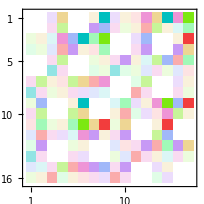

```mathematica
TensorLoad["TS"]//ComplexMatrixPlot
```

```mathematica
StringTake
```

```mathematica
Module[{TS,W},
TS=TensorLoad["TS"];
W={0.5,0.5,0.5,0.5};
Column@NestList[Chop[Normalize@(Normalize[(#/#⟦1⟧&)@(TS.#)]+#),0.00001]&,W,24]]
```

{0.5,0.5,0.5,0.5}
{0.722112,0.396579-0.162766 ⅈ,0.396579-0.162766 ⅈ,0.0710462-0.325533 ⅈ}
{0.645955,0.38898+0.0220608 ⅈ,0.38898+0.0220608 ⅈ,-0.107833-0.517233 ⅈ}
{0.466166,0.478404-0.0877772 ⅈ,0.478404-0.0877772 ⅈ,-0.424201-0.35999 ⅈ}
{0.444117,0.465744-0.176444 ⅈ,0.465744-0.176444 ⅈ,-0.531554-0.155278 ⅈ}
{0.457211,0.442602-0.230017 ⅈ,0.442602-0.230017 ⅈ,-0.539883-0.0432987 ⅈ}
{0.473857,0.431876-0.251272 ⅈ,0.431876-0.251272 ⅈ,-0.52549+0.00331879 ⅈ}
{0.487587,0.428722-0.257076 ⅈ,0.428722-0.257076 ⅈ,-0.512058+0.0165461 ⅈ}
{0.496167,0.429092-0.256599 ⅈ,0.429092-0.256599 ⅈ,-0.503643+0.015351 ⅈ}
{0.500298,0.43051-0.254261 ⅈ,0.43051-0.254261 ⅈ,-0.499628+0.00988252 ⅈ}
{0.501585,0.43181-0.252064 ⅈ,0.43181-0.252064 ⅈ,-0.498395+0.00477717 ⅈ}
{0.501488,0.432642-0.250639 ⅈ,0.432642-0.250639 ⅈ,-0.498508+0.00147694 ⅈ}
{0.500959,0.433042-0.249948 ⅈ,0.433042-0.249948 ⅈ,-0.49904-0.000120401 ⅈ}
{0.500462,0.433166-0.249734 ⅈ,0.433166-0.249734 ⅈ,-0.499537-0.000614227 ⅈ}
{0.500143,0.433156-0.249751 ⅈ,0.433156-0.249751 ⅈ,-0.499857-0.00057422 ⅈ}
{0.499988,0.433105-0.24984 ⅈ,0.433105-0.24984 ⅈ,-0.500012-0.00036941 ⅈ}
{0.499941,0.433057-0.249923 ⅈ,0.433057-0.249923 ⅈ,-0.500059-0.000177987 ⅈ}
{0.499945,0.433026-0.249976 ⅈ,0.433026-0.249976 ⅈ,-0.500055-0.0000548589 ⅈ}
{0.499964,0.433012-0.250002 ⅈ,0.433012-0.250002 ⅈ,-0.500036}
{0.499982,0.433008-0.250009 ⅈ,0.433008-0.250009 ⅈ,-0.500018+0.000020516 ⅈ}
{0.499994,0.433008-0.250009 ⅈ,0.433008-0.250009 ⅈ,-0.500006+0.0000205157 ⅈ}
{0.5,0.433009-0.250006 ⅈ,0.433009-0.250006 ⅈ,-0.5+0.0000136772 ⅈ}
{0.500002,0.433011-0.250003 ⅈ,0.433011-0.250003 ⅈ,-0.499998}
{0.500001,0.433013-0.25 ⅈ,0.433013-0.25 ⅈ,-0.499999}
{0.5,0.433013-0.25 ⅈ,0.433013-0.25 ⅈ,-0.5}

```mathematica
Module[{TS,W},
TS=Flatten[TensorLoad["TS"],{{2,4,8,6},{1,3,7,5}}];
W={0.5,0.5,0.5,0.5};
Column@NestList[Chop[Normalize[(#/#⟦1⟧&)@(TS.#)],0.00001]&,W,10]]
```

{0.5,0.5,0.5,0.5}
{0.645497,0.129099-0.258199 ⅈ,0.129099-0.258199 ⅈ,-0.387298-0.516398 ⅈ}
{0.223607,-0.67082,-0.67082,0.223607}
{0.634172,-0.0514193-0.308516 ⅈ,-0.0514193-0.308516 ⅈ,-0.599892+0.205677 ⅈ}
{0.0780869,0.702782,0.702782,0.0780869}
{0.63265,0.0175195-0.315352 ⅈ,0.0175195-0.315352 ⅈ,-0.628757-0.0700782 ⅈ}
{0.0261712,-0.706622,-0.706622,0.0261712}
{0.632477,-0.00585426-0.31613 ⅈ,-0.00585426-0.31613 ⅈ,-0.632044+0.0234171 ⅈ}
{0.00872905,0.707053,0.707053,0.00872905}
{0.632458,0.00195196-0.316217 ⅈ,0.00195196-0.316217 ⅈ,-0.63241-0.00780783 ⅈ}
{0.00290988,-0.707101,-0.707101,0.00290988}

```mathematica
Module[{TS,W},
TS=Flatten[TensorLoad["TS"],{{2,4,8,6},{1,3,7,5}}];
W={0.5,0.5,0.5,0.5};
Normalize[(#/#⟦1⟧&)@(TS.#)]&@W]
```

{0.645497+0. ⅈ,0.129099-0.258199 ⅈ,0.129099-0.258199 ⅈ,-0.387298-0.516398 ⅈ}

## Code

#### I/O System

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### SYSVD

```mathematica
SYSVD[A_]:=Module[{U,S,V,Θ},
{U,S,V}=SingularValueDecomposition[A];
Θ=MatrixPower[Transpose[V].U,-1/2];
{U.Θ,S,V.Θ}];
```